```mathematica
loadDataInitial=SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.csv"]
```

Dataset[<>]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.wxf", loadDataInitial]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\alldata.wxf

```mathematica
loadDataInitial = Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.wxf"]
```

Dataset[<>]

```mathematica
MissingValues
```

```mathematica
dataWithMissing = SynthesizeMissingValues[
Map[{#Date, #HE, #MWh}&,    Normal[loadDataInitial]]

];
```

```mathematica
timeseries = TimeSeries[
Apply[
	Function[
		{date, he, mwh},
		{DateObject[date, TimeObject[he], TimeZone->"America/New_York"], mwh}
	],
	dataWithMissing,
{1}
]
]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\timeseries.wxf", timeseries]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\timeseries.wxf

```mathematica
loadTimeSeries=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\timeseries.wxf"]
```

TimeSeries[…]

```mathematica
loadTimeSeriesResampled=TimeSeriesResample[loadTimeSeries,"Hour"]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf", loadTimeSeriesResampled]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\LoadtimeseriesResampled.wxf

```mathematica
Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
RegularlySampledQ[loadTimeSeriesResampled]
```

True

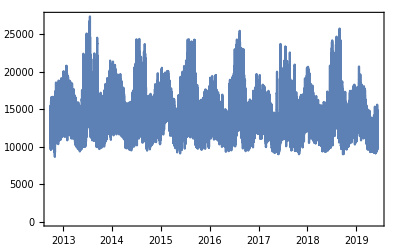

```mathematica
DateListPlot[loadTimeSeriesResampled]
```